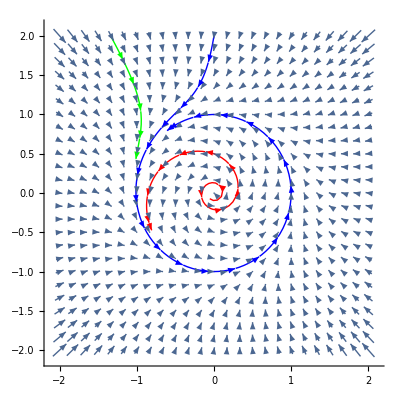

```mathematica
StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r(1-r^2),1},{r,θ}->{x,y}],{x,-2,2},{y,-2,2},VectorStyle->Automatic,StreamStyle->Blue,StreamPoints->{{{{0,2},Automatic},{{-1,3},Green},{{0,.5},Red},{{0,-1},Orange},{{-1,.5},Green},{{2,4},Yellow}}},Axes->True,Frame->None,VectorPoints->Fine]
```

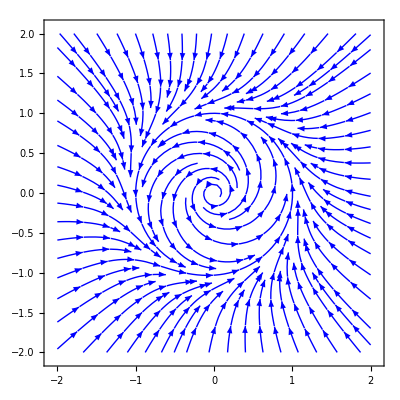

```mathematica
StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r(1-r^2),1},{r,θ}->{x,y}],{x,-2,2},{y,-2,2},VectorStyle->Automatic,StreamStyle->Blue]
```

-2

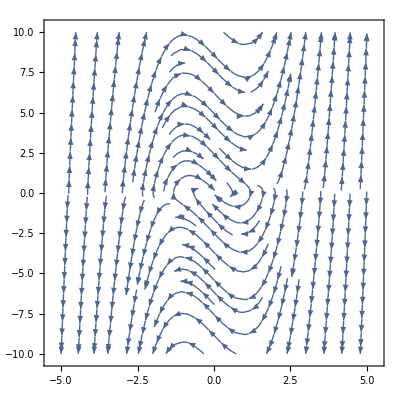

```mathematica
a=-2
G1=StreamPlot[{v,a(1-u^2)v-u},{u,-5,5},{v,-10,10}]
```

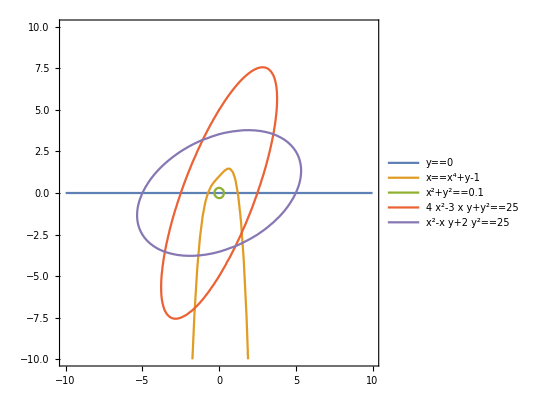

```mathematica
G2=ContourPlot[{y==0,x==y-(1-x^4),x^2+y^2==.1,4x^2+y^2-3*x*y==25,x^2+2y^2-x*y==25},{x,-10,10},{y,-10,10},AspectRatio->1,PlotLegends->"Expressions"]
```

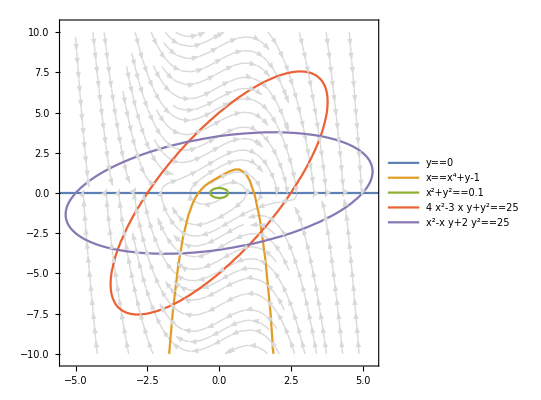

```mathematica
Show[G1,G2]
```

```mathematica
a=2;e=2;s=NDSolve[{x''[t]+e*(x'[t])^3+x[t]==0,x[0]==a,x'[0]==0},x,{t,0,50}]
```

{{x→InterpolatingFunction[{{0., 50.}}, <>]}}

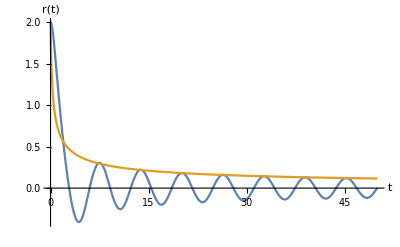

```mathematica
Plot[{Evaluate[x[t]]/.s,Sqrt[4/3/(e*t+4/(3a^2))]},{t,0,50},PlotRange->All,AxesLabel->{"t","r(t)"}]
```

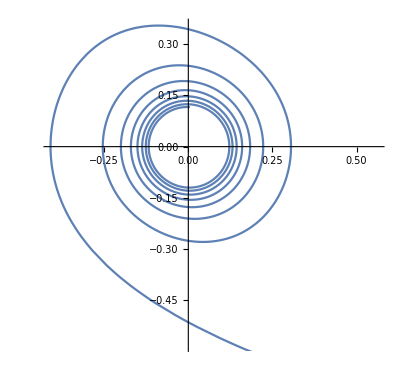

```mathematica
ParametricPlot[Evaluate[{x[t],x'[t]}/.s],{t,0,50}]
```

```mathematica
Solve[{B-x-((x*y)/(1+q*x^2))==0,A-((x*y)/(1+q*x^2))==0},{x,y}]
```

{{x→-A+B,y→(-A-A^3 q+2 A^2 B q-A B^2 q)/(A-B)}}

```mathematica
ClearAll["Global`*"];FullSimplify[(-A-A^3 q+2 A^2 B q-A B^2 q)/(A-B)]
```

A (1/(-A+B)-A q+B q)

```mathematica
JacobianMatrix[f_List?VectorQ,x_List]:=Outer[D,f,x]/;Equal@@(Dimensions/@{f,x})

JacobianDeterminant[f_List?VectorQ,x_List]:=Det[JacobianMatrix[f,x]]/;Equal@@(Dimensions/@{f,x})
```

```mathematica
a={B-x-(x*y)/(1+q*x^2),A-(x*y)/(1+q*x^2)};
b={x,y};
JacobianMatrix[a,b]//MatrixForm
JacobianDeterminant[a,b]//MatrixForm
```

(-1+(2 q x^2 y)/((1+q x^2)^2)-y/(1+q x^2) | -x/(1+q x^2)
(2 q x^2 y)/((1+q x^2)^2)-y/(1+q x^2) | -x/(1+q x^2))

x/((1+q x^2)^4)+(3 q x^3)/((1+q x^2)^4)+(3 q^2 x^5)/((1+q x^2)^4)+(q^3 x^7)/((1+q x^2)^4)

```mathematica
x=-A+B;y=A (-1-(A-B)^2 q);
FullSimplify[(2 q x^2 y)/((1+q x^2)^2)-y/(1+q x^2)-1]
FullSimplify[(2 q x^2 y)/((1+q x^2)^2)-y/(1+q x^2)]
FullSimplify[-x/(1+q x^2)]
```

-1+A (-1+2/(1+(A-B)^2 q))

A (-1+2/(1+(A-B)^2 q))

(A-B)/(1+(A-B)^2 q)

```mathematica
M=({{-1+A (-1+2/(1+(A-B)^2 q)), (A-B)/(1+(A-B)^2 q)}, {A (-1+2/(1+(A-B)^2 q)), (A-B)/(1+(A-B)^2 q)}})
```

{{-1+A (-1+2/(1+(A-B)^2 q)),(A-B)/(1+(A-B)^2 q)},{A (-1+2/(1+(A-B)^2 q)),(A-B)/(1+(A-B)^2 q)}}

```mathematica
FullSimplify[Tr[M]](*<0 so unstable pt*)
```

-1-A+(3 A-B)/(1+(A-B)^2 q)

```mathematica
FullSimplify[Det[M]](*A>B so that det<0*)
```

(-A+B)/(1+(A-B)^2 q)

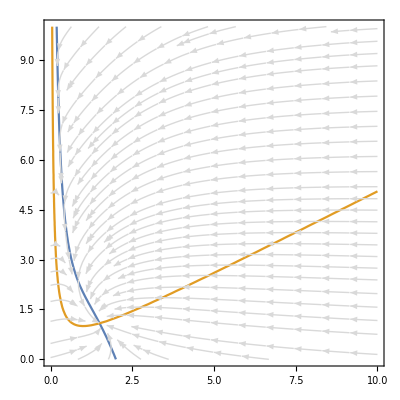

```mathematica
ClearAll["Global`*"];A=0.5;B=2;q=1;
X1=ContourPlot[{B-i-(i*j)/(1+q*i^2)==0,A-(i*j)/(1+q*i^2)==0},{i,0,10},{j,0,10}];
X2=StreamPlot[{B-i-(i*j)/(1+q*i^2),A-(i*j)/(1+q*i^2)},{i,0,10},{j,0,10},StreamStyle->LightGray];Show[X1,X2]
```

```mathematica
f[a_][x_]:=a*x-1.19 x^3;
cps[a_]=x/.Quiet[Solve[D[f[a][x],x]==0,x],Solve::ratnz];
criticalOrbits[a_,cp_]:=Module[{try},If[Head[cp]===Real,try=NestWhileList[f[a],cp,Abs[#]<100&,1,500];
If[Abs[Last[try]]≥100,try={},try=Drop[{a,#}&/@try,100]],{}]];
points[k_]:=Partition[Flatten[Table[criticalOrbits[a,cps[a][[k]]],{a,-2,4,0.002}]],2];
Graphics[{Opacity[0.02],PointSize[0.002],Table[{ColorData[1,k],Point[points[k]]},{k,1,Length[cps[a]]}]},Frame->True]
```

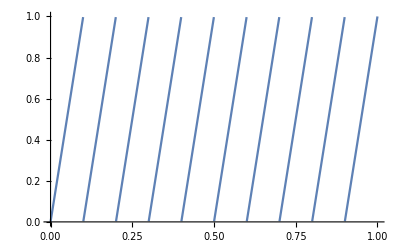

```mathematica
Plot[Mod[10*x,1],{x,0,1}]
```